## Calculate average photon absorption efficiency of silicon (using Geant4 reflectivity calculation and empirical transmission measurements)

### Load in refractive index data

```mathematica
rIdxFn=NotebookDirectory[]<>"silicon-refr-idx-ev-n-k.tab";
rawRefrIdx=Transpose[Import[rIdxFn]];
```

```mathematica
energies=rawRefrIdx[[1]];
refrIdxArray=rawRefrIdx[[2]]+I*rawRefrIdx[[3]];
```

### Define the various functions from the Geant4 `GetReflectivity` method

```mathematica
cosPhi[θ_]:=Sqrt[1-Sin[θ]^2/refrIdxArray];
teTrans[θ_]:=(Cos[θ]-refrIdxArray*cosPhi[θ])/(Cos[θ]+refrIdxArray*cosPhi[θ]);
trTrans[θ_]:=(refrIdxArray*Cos[θ]-cosPhi[θ])/(refrIdxArray*Cos[θ]+cosPhi[θ]);
reflection[θ_,ε_]:=(Abs[teTrans[θ]]^2+ε^2 Abs[trTrans[θ]]^2)/(1+ε^2);
```

### Average over the angle of incidence θ∈[0,π/2] and ε=E_(||)/E_⊥. Note that the reflection is symmetric about E_(||)/E_⊥, so we only need to integrate ε ∈ [0,1] and then ... ?

```mathematica
Subscript[θ, max]=π/2;
averageReflection=1/Subscript[θ, max] NIntegrate[reflection[t,e],{t,0,Subscript[θ, max]},{e,0,1}];
```

```mathematica
averageReflection
```

{0.769533,0.773324,0.775272,0.77773,0.7802,0.781779,0.780859,0.781808,0.779598,0.777363,0.775061,0.771309,0.769326,0.76529,0.762786,0.756884,0.751777,0.743373,0.73434,0.723828,0.713644,0.704657,0.696166,0.688981,0.682464,0.67667,0.671407,0.667456,0.662794,0.659515,0.655621,0.653272,0.65074,0.64889,0.646277,0.644918,0.643244,0.641964,0.640956,0.639868,0.638912,0.63828,0.638098,0.637738,0.638289,0.639588,0.641469,0.643164,0.646798,0.651481,0.656623,0.660614,0.662761,0.661024,0.65648,0.648955,0.639899,0.629527,0.620225,0.611327,0.60293,0.595564,0.588693,0.582051,0.576079,0.570602,0.565609,0.560516,0.556224,0.551633,0.54757,0.543487,0.539819,0.536151,0.532434,0.529507,0.526062,0.523011,0.520105,0.517105,0.514452,0.511646,0.50901,0.506341,0.503855,0.501556,0.499164,0.496962,0.494953,0.492929,0.490818,0.488759,0.486981,0.485266,0.483464,0.4818,0.480125,0.478593,0.476973,0.475499,0.473938,0.472603,0.471262,0.469833,0.468476,0.467201,0.465991,0.464801,0.463629,0.462485,0.46136,0.460255,0.459104,0.458105,0.457062,0.456047,0.455004,0.454083,0.453133,0.452214,0.451352,0.450435,0.449584,0.448756,0.448168,0.447179,0.446431,0.445707,0.444858}

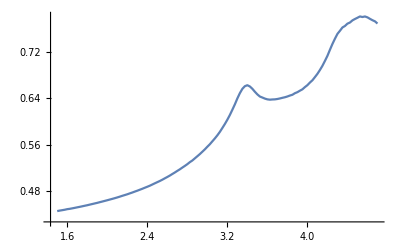

```mathematica
energyAndReflection=Transpose[{energies,averageReflection}];
ListPlot[energyAndReflection,Joined->True]
```